```mathematica
p[x__]:=(PDF[MultinormalDistribution[{5,5},{{1.5,0.5},{0.5,1.5}}],{x}]+PDF[MultinormalDistribution[{15,15},{{1.5,-0.5},{-0.5,1.5}}],{x}])[[1]]
```

```mathematica
v[x_]:=p[x]^(-0.95)
```

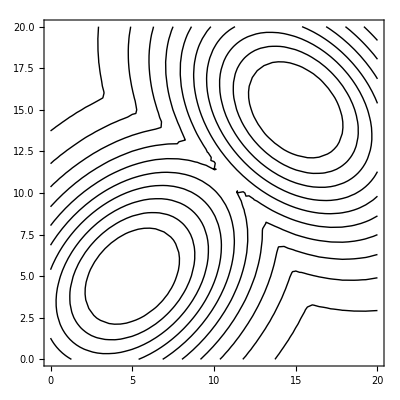

```mathematica
gMain=ContourPlot[v[{x,y}] p[{x,y}],{x,0,20},{y,0,20},ContourStyle->Black,Contours->10,ContourShading->None,PlotRange->Full]
```

```mathematica
fStep[x_,y_,σ_]:=RandomVariate[MultinormalDistribution[{x,y},σ IdentityMatrix[2]],1][[1]]
fStepAndAccept[x_,y_,σ_,p_,v_]:=Module[{new=fStep[x,y,σ],r=RandomReal[]},If[(p[new] v[new])/(p[{x,y}] v[{x,y}])>r,new,{x,y}]]
fMetropolis[n_Integer,x0_,y0_,σ_,p_,v_]:=NestList[fStepAndAccept[#[[1]],#[[2]],σ,p,v]&,{x0,y0},n]
```

```mathematica
ldata=fMetropolis[10000,5,5,1,p,v];
```

```mathematica
weights=(1/v[#])&/@ldata;
```

```mathematica
aDist=WeightedData[ldata,weights]
```

WeightedData[…]

```mathematica
Variance[aDist]
```

{26.6095,26.7124}

```mathematica
Mean[aDist]
```

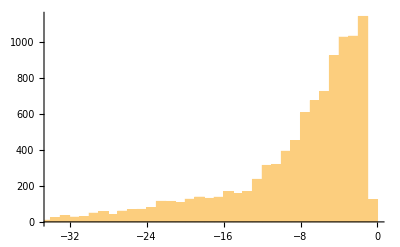

```mathematica
Histogram[Log10@weights]
```

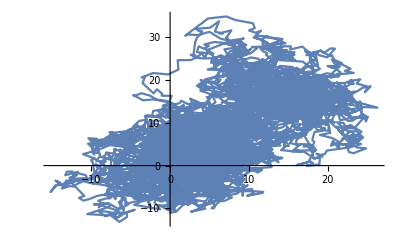

```mathematica
ListLinePlot[ldata]
```

### Sampling from points in proportion to their weights

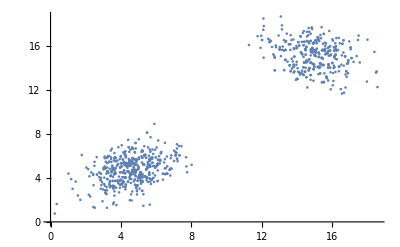

```mathematica
ListPlot[RandomChoice[aDist,1000]]
```

### Effective sample size

```mathematica
fESS[weights_]:=Module[{w=weights/Total[weights]},1/Total[w^2]]
```

## Try more complex example

```mathematica
p[x__]:=(PDF[MultinormalDistribution[{5,5},{{1.5,0.5},{0.5,1.5}}],{x}]+PDF[MultinormalDistribution[{15,15},{{1.5,-0.5},{-0.5,1.5}}],{x}]+PDF[MultinormalDistribution[{5,25},{{1.5,1},{1,1.5}}],{x}]+
PDF[MultinormalDistribution[{25,5},{{0.5,0.3},{0.3,0.5}}],{x}])[[1]]
```

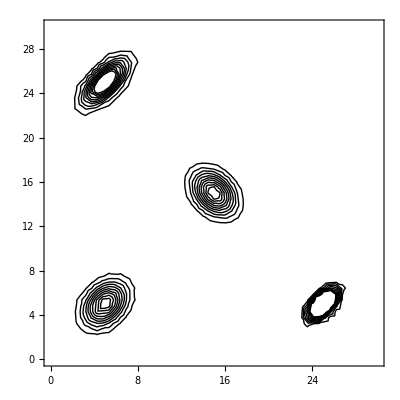

```mathematica
gMain=ContourPlot[p[{x,y}],{x,0,30},{y,0,30},ContourStyle->Black,Contours->10,ContourShading->None,PlotRange->Full]
```

```mathematica
ldata=fMetropolis[10000,5,5,1,p,v];
weights=(1/v[#])&/@ldata;
```

```mathematica
ListLinePlot[ldata]
```

```mathematica
aDist=WeightedData[ldata,weights]
```

WeightedData[…]

```mathematica
fESS[weights]
```

854.963

```mathematica
ListPlot[RandomChoice[aDist,1000]]
```

### Log Eggbox

```mathematica
p[x__]:=If[And[And[x[[1]]>0,x[[2]]>0],And[x[[1]]<10π,x[[2]]<10π]],(2+Cos[x[[1]]/2]Cos[x[[2]]/2])^5,Exp[-100]]
```

```mathematica
ldata=fMetropolis[20000,5,5,1,p,v];
weights=(1/v[#])&/@ldata;
```

```mathematica
aDist=WeightedData[ldata,weights]
```

WeightedData[…]

```mathematica
ListLinePlot[ldata]
```

```mathematica
fESS[weights]
```

10008.6

```mathematica
samples=RandomChoice[aDist,10000];
pdf=p/@samples;
```

```mathematica
ListPointPlot3D[Thread[{samples[[All,1]],samples[[All,2]],pdf}]]
```

## Eggbox proper

```mathematica
p[x__]:=If[And[And[x[[1]]>0,x[[2]]>0],And[x[[1]]<10π,x[[2]]<10π]],Exp[(2+Cos[x[[1]]/2]Cos[x[[2]]/2])^5],Exp[-10]]
```

```mathematica
v[x_]:=p[x]^(-0.99)
```

```mathematica
gMain=ContourPlot[v[{x,y}] p[{x,y}],{x,0,10Pi},{y,0,10Pi},ContourStyle->Black,Contours->10,ContourShading->None,PlotRange->Full]
```

```mathematica
Plot3D[v[{x,y}] p[{x,y}],{x,0,10Pi},{y,0,10Pi},PlotRange->Full]
```

```mathematica
fStep[x_,y_,σ_]:=Mod[RandomVariate[MultinormalDistribution[{x,y},σ IdentityMatrix[2]],1][[1]],10 Pi]
```

```mathematica
ldata=fMetropolis[20000,5,5,1,p,v];
weights=(1/v[#])&/@ldata;
```

```mathematica
aDist=WeightedData[ldata,weights]
```

WeightedData[…]

```mathematica
ListPlot[ldata]
```

```mathematica
fESS[weights]
```

180.839

```mathematica
samples=RandomChoice[aDist,Round@fESS[weights]];
pdf=p/@samples;
```

```mathematica
ListPlot[samples]
```

## Chris Holmes example

```mathematica
mu={-3,0,3,6};
```

```mathematica
fRandomMixtureNormal[μ__,σ_]:=Module[{k=Length@μ,mode},mode=RandomChoice[Range@k];RandomVariate[NormalDistribution[μ[[mode]],σ],{1}][[1]]]
```

```mathematica
y=Table[fRandomMixtureNormal[mu,0.55],{i,1,100,1}];
```

```mathematica
fPosterior[μ__,σ_,y__]:=Product[Sum[0.25 PDF[NormalDistribution[μ[[i]],σ],y[[j]]],{i,1,4,1}],{j,1,Length@y,1}]
```

```mathematica
fPosterior1[μ__]:=fPosterior[μ,0.55,y]
fv[x__]:=fPosterior1[x]^(-0.9)
```

```mathematica
fStep[x_,y_,z_,w_,σ_]:=RandomVariate[MultinormalDistribution[{x,y,z,w},σ IdentityMatrix[4]],1][[1]]
fStepAndAccept[x_,y_,z_,w_,σ_,p_,v_]:=Module[{new=fStep[x,y,z,w,σ],r=RandomReal[]},If[(p[new] v[new])/(p[{x,y,z,w}] v[{x,y,z,w}])>r,new,{x,y,z,w}]]
fMetropolis[n_Integer,x0_,y0_,z0_,w0_,σ_,p_,v_]:=NestList[fStepAndAccept[#[[1]],#[[2]],#[[3]],#[[4]],σ,p,v]&,{x0,y0,z0,w0},n]
```

```mathematica
fDist[μ__]:=MixtureDistribution[{0.25,0.25,0.25,0.25},{NormalDistribution[μ[[1]],0.55],NormalDistribution[μ[[2]],0.55],NormalDistribution[μ[[3]],0.55],NormalDistribution[μ[[4]],0.55]}]
```

```mathematica
fPosterior1[μ_]:=Likelihood[fDist[μ],y]
```

```mathematica
data=Flatten[ParallelTable[fMetropolis[100000,1,1,1,1,1,fPosterior1,fv],{i,1,12,1}],1];
```

$Aborted

```mathematica
weights=ParallelTable[(1/fv[data[[i]]]),{i,1,Length@data,1}];
```

$Aborted

```mathematica
aDist=WeightedData[data,weights]
```

WeightedData[…]

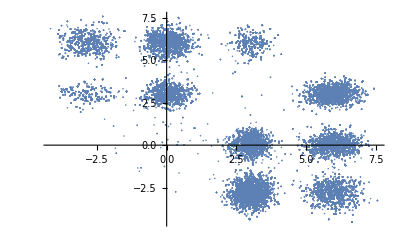

```mathematica
ListPlot[data[[All,{1,2}]]]
```

```mathematica
samples=RandomChoice[aDist,Round@fESS[weights]];
```

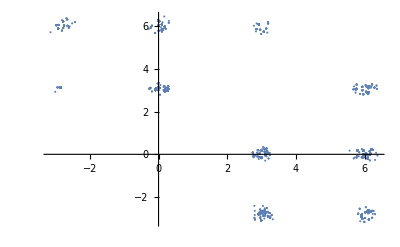

```mathematica
ListPlot[samples[[All,{1,2}]],PlotRange->Full]
```

## HMC within importance sampling -- eggbox --- something’s not correct here...

```mathematica
D[(2+Cos[x/2]Cos[y/2])^5,y]
```

-5/2 Cos[x/2] (2+Cos[x/2] Cos[y/2])^4 Sin[y/2]

### derivatives of 0.01 Log p

```mathematica
dX[x_,y_]:=If[And[And[x>0,y>0],And[x<10π,y<10π]],-5/2 0.01 Cos[y/2] (2+Cos[x/2] Cos[y/2])^4 Sin[x/2],0]
dY[x_,y_]:=If[And[And[x>0,y>0],And[x<10π,y<10π]],-5/2 0.01Cos[x/2] (2+Cos[x/2] Cos[y/2])^4 Sin[y/2],0]
fDerivative[x_,y_]:={dX[x,y],dY[x,y]}
logP[x__]:=If[And[And[x[[1]]>0,x[[2]]>0],And[x[[1]]<10π,x[[2]]<10π]],0.01(2+Cos[x[[1]]/2]Cos[x[[2]]/2])^5,-100000]
```

```mathematica
fLeapFrogStep[θ_,m_,ϵ_]:=Module[{grad,x,θ1,m1,grad1},grad=fDerivative[θ[[1]],θ[[2]]];m1=m+0.5 ϵ grad; θ1=θ+ϵ m1;grad1=fDerivative[θ1[[1]], θ1[[2]]];m1=m1+0.5 ϵ grad1;{θ1,m1}]
fLeapFrogSteps[θ_,m_,ϵ_,L_Integer]:=NestList[fLeapFrogStep[#[[1]],#[[2]],ϵ]&,{θ,m},L][[-1]]
fHMCStep1[θ_,ϵ_,L_Integer,logP1_]:=Module[{m=RandomVariate[NormalDistribution[0,1],2],theta,m1,r=RandomReal[],res},res=fLeapFrogSteps[θ,m,ϵ,L];
theta=res[[1]];m1=res[[2]];
Print[Exp[logP1[θ]-logP1[theta]+PDF[MultinormalDistribution[{0,0},IdentityMatrix[2]],m1]-PDF[MultinormalDistribution[{0,0},IdentityMatrix[2]],m]]];
If[logP1[theta]==-100000,θ,If[Exp[logP1[θ]-logP1[theta]+PDF[MultinormalDistribution[{0,0},IdentityMatrix[2]],m1]-PDF[MultinormalDistribution[{0,0},IdentityMatrix[2]],m]]>r,theta,θ]]]
fHMC1[n_Integer,θ0_,ϵ_,L_Integer,logP1_]:=NestList[fHMCStep1[#,ϵ,L,logP1]&,θ0,n]
```

```mathematica
fHMCStep1[{15,15},0.1,10,logP]
```

1.00061

{15.224,14.6625}

```mathematica
ldata=fHMC1[2000,{5,5},0.1,10,logP];
```

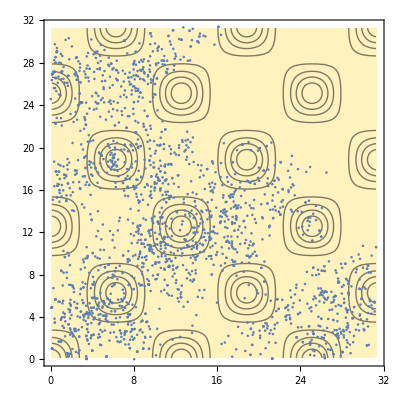

```mathematica
Show[ContourPlot[logP[{x,y}],{x,0,10Pi},{y,0,10 Pi}],ListPlot[ldata]]
```

```mathematica
p[x__]:=If[And[And[x[[1]]>0,x[[2]]>0],And[x[[1]]<10π,x[[2]]<10π]],Exp[(2+Cos[x[[1]]/2]Cos[x[[2]]/2])^5],Exp[-10]]
```

```mathematica
v[x_]:=p[x]^(-0.99)
```

```mathematica
weights=(1/v[#])&/@ldata;
```

```mathematica
aDist=WeightedData[ldata,weights]
```

WeightedData[…]

```mathematica
fESS[weights]
```

22.7067

```mathematica
samples=RandomChoice[aDist,Round@fESS[weights]];
```

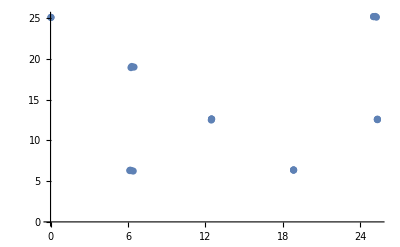

```mathematica
ListPlot[samples]
```

```mathematica
gMain=ContourPlot[0.01logP[{x,y}],{x,0,10Pi},{y,0,10Pi},ContourStyle->Black,Contours->10]
```